# SHOOTING ALGORITHM

### Part a) Fully define the competitive equilibrium

A competitive equilibrium consists of A) prices , B) allocations for the household , C) allocations for the firm  and D) firm and household profits , such that:
1) Given prices A) , the allocation of the household B)  solves the household problem -Graphics-
2) Given prices A) , the allocation of the firm C)  solves the firm problem -Graphics- where, -Graphics-
3) Markets clear: 
				-Graphics-(Goods Market)
				-Graphics-(Labor Market)
				-Graphics-(Capital Market)
4) Firm profits equal household profits: -Graphics-

### Part b. Find the first order conditions. Be sure to show all working.

The set up for the problem is as follows:
The representative household solves:
						-Graphics-
subject to:
						-Graphics-
The representative firm solves:
						-Graphics-
where, -Graphics-
Prices adjust so that markets clear:
						-Graphics-(Goods Market)
						-Graphics-(Labor Market)
						-Graphics-(Capital Market)
To find the FOC for the household we will substitute the budget constraint into the utility function. From the capital accumulation constraint rearrange to get I_t= K_(t+1)-(1-δ)K_t. Substitute I_t into -Graphics-  to get 
C_t + K_(t+1)-(1-δ)K_t= w_tL_t + r_tK_t + π_t
C_t = w_tL_t + r_tK_t + π_t - K_(t+1)+(1-δ)K_t
C_t = w_tL_t +(1+ r_t-δ)K_t + π_t - K_(t+1)
L_t = 1 so,
C_t = w_t +(1+ r_t-δ)K_t + π_t - K_(t+1)
Now substitute C_t into the utility function to get:
∑_(t=0)^∞ β^t log(w_t+(1+r_t-δ)K_t+π_t-K_(t+1))
Now differentiate with respect to K_(t+1). Notice that only terms C_t and C_(t+1) contain the term K_(t+1) so from the entire sum we can focus only on those terms. So,
U = β^t log(w_t+(1+r_t-δ)K_t+π_t-K_(t+1)) + β^(t+1)log(w_(t+1)+(1+r_(t+1)-δ)K_(t+1)+π_(t+1)-K_(t+2))
Now we can differentiate with respect to K_(t+1) and set equal to 0.

```mathematica
U = β^t*Log[Subscript[w, t]+(1+Subscript[r, t]-δ)*Subscript[K, t]+Subscript[π, t]-Subscript[K, t+1]]+β^(t+1)*Log[Subscript[w, t+1]+(1+Subscript[r, t+1]-δ)*Subscript[K, t+1]+Subscript[π, t+1]-Subscript[K, t+2]];
D[U,Subscript[K, t+1]]==0
```

-β^t/(-K_(1+t)+π_t+K_t (1-δ+r_t)+w_t)+(β^(1+t) (1-δ+r_(1+t)))/(-K_(2+t)+π_(1+t)+K_(1+t) (1-δ+r_(1+t))+w_(1+t))==0

The output from differentiation above is:
					-Graphics-
We can rearrange to get:
β^t/(w_t+(1+r_t-δ)K_t+π_t-K_(t+1)) = (β^(t+1)(1+r_(t+1)-δ))/(w_(t+1)+(1+r_(t+1)-δ)*K_(t+1)+π_(t+1)-K_(t+2))
Then we divide both sides by β^t to get:
1/(w_t+(1+r_t-δ)K_t+π_t-K_(t+1)) = (β(1+r_(t+1)-δ))/(w_(t+1)+(1+r_(t+1)-δ)*K_(t+1)+π_(t+1)-K_(t+2))
Then we can realise that the denominator of the LHS is C_t and the denominator of the RHS is C_(t+1) so,
1/C_t = (β(1+r_(t+1)-δ))/(C_(t+1))
Then multiply both sides by C_(t+1) to get:
(C_(t+1))/C_t = β(1+r_(t+1)-δ)
This gives us the Euler equation

To find the FOC for the firm we take the profit maximising condition and substitute Y_t into it. So we get:
π_t^f = max_(L_t^f,K_t^f)  (K_t^f)^α(AL_t^f)^(1-α)- w_tL_t^f - r_tK_t^f
Then we can differentiate with respect to L_t^f and K_t^f to get the first order conditions.

```mathematica
Profit=(Subscript[K, t])^α(A*Subscript[L, t])^(1-α)-Subscript[w, t] Subscript[L, t]-Subscript[r, t] Subscript[K, t];
D[Profit,Subscript[L, t]]==0
D[Profit,Subscript[K, t]]==0
```

A (1-α) K_t^α (A L_t)^-α-w_t==0

α K_t^(-1+α) (A L_t)^(1-α)-r_t==0

The output from differentiation in Mathematica gives us:
						-Graphics-
We can rearrange this to get:
w_t = A (1-α) (K_t^f)^α (AL_t^f)^-α = A (1-α) (K_t^f)^α (1/AL_t^f)^α = A (1-α) (K_t^f/AL_t^f)^α
r_t = α (K_t^f)^(-1+α) (AL_t^f)^(1-α) = α (1/K_t^f)^(1-α) (AL_t^f)^(1-α) = α (AL_t^f/K_t^f)^(1-α)

### Part C. The solution to the growth model we studied in class was characterized by the Euler equation written only in terms of capital stocks. Write out this Euler equation.

From above we know that the Euler equation is : (C_(t+1))/C_t = β(1+r_(t+1)-δ).
We know that Y_t = C_t + I_t,  I_t= K_(t+1)-(1-δ)K_t,  r_t = α (AL_t/K_t)^(1-α) and  r_(t+1) = α ((AL_(t+1))/(K_(t+1)))^(1-α).
C_t = Y_t - I_t = (K_t)^α(AL_t)^(1-α) - (K_(t+1)-(1-δ)K_t)
Similarly, for C_(t+1):
C_(t+1) = (K_(t+1))^α(AL_(t+1))^(1-α) - (K_(t+2)-(1-δ)K_(t+1))
Substituting this into the Euler equation:
((K_(t+1))^α(AL_(t+1))^(1-α)-(K_(t+2)-(1-δ)K_(t+1)))/((K_t)^α(AL_t)^(1-α)-(K_(t+1)-(1-δ)K_t)) = β(1+α(A/(K_(t+1)))^(1-α)-δ)
We know that L is equal to 1 so:
((K_(t+1))^α(A)^(1-α)-K_(t+2)+(1-δ)K_(t+1))/((K_t)^α(A)^(1-α)-K_(t+1)+(1-δ)K_t) = β(1+α(A/(K_(t+1)))^(1-α)-δ)
which is the Euler equation written only in terms of capital stock.

### Part d. Recall, a steady state of the above problem was an equilibrium where all variables were constant. Use the first order condition above to solve for the steady state level of capital K^*

A steady state is a competitive equilibrium where all variables are constant:
K_(t+1) = K_t = K^*
C_(t+1) = C_t = C^*
r_(t+1) = r_t = r^*
w_(t+1) = w_t = w^*
From the Euler equation in steady state it is true that:
(C_(t+1))/C_t = β(1+r_(t+1)-δ) --> C^*/C^* = β(1+r^*-δ) hence,
1 = β(1 + r^* - δ) Divide both sides by β
1/β = 1 + r^* - δ  Move  r^* to the LHS and 1/β to the RHS
r^* = 1/β - 1 + δ
From the first order condition we know:
r_t = α (A/K_t)^(1-α) --> r^* = α (A/K^*)^(1-α)
This implies that in the steady state:
1/β - 1 + δ = α (A/K^*)^(1-α) Divide both sides by α
(1/β-1+δ)/α = (A/K^*)^(1-α)  Expand the RHS
(1/β-1+δ)/α = A^(1-α)/((K^*)^(1-α))  Multiply both sides by (K^*)^(1-α)
(K^*)^(1-α)(1/β-1+δ)/α = A^(1-α)  Multiply both sides by α/(1/β-1+δ)
(K^*)^(1-α) = A^(1-α) (α/(1/β-1+δ))  Take both sides to the power of 1/(1-α)
K^* = A  (α/(1/β-1+δ))^(1/(1-α))  We have found the steady state level of capital K^*

### Part e. Assume that the model converges to the steady state after T=70 periods.Write code that will allow you to solve the above model using the shooting algorithm that we studied in class. For the parameters assume α=0.33,β=0.98,δ=0.1,A=1 and K0=0.1.Plot the evolution of the capital stock you find.

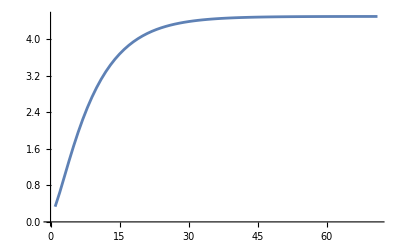

{0.333384,0.646649,0.988576,1.33101,1.65924,1.96593,2.24784,2.50411,2.73523,2.94243,3.12736,3.29183,3.4377,3.56679,3.68081,3.78138,3.86996,3.94792,4.01645,4.07666,4.12953,4.17592,4.2166,4.25228,4.28354,4.31094,4.33493,4.35595,4.37435,4.39046,4.40456,4.41691,4.42771,4.43716,4.44543,4.45267,4.459,4.46454,4.46938,4.47362,4.47732,4.48057,4.4834,4.48588,4.48805,4.48995,4.4916,4.49305,4.49432,4.49543,4.4964,4.49725,4.49798,4.49863,4.49919,4.49969,4.50011,4.50049,4.50081,4.50109,4.50134,4.50155,4.50173,4.50188,4.50201,4.50211,4.5022,4.50227,4.50232,4.50235,4.50237}

```mathematica
α=0.33;β=0.98;δ=0.1;A=1;
H[t_]:=((1-δ) Subscript[k, 1+t]+Subscript[k, 1+t]^α A^(1-α)-Subscript[k, 2+t])/((1-δ) Subscript[k, t]+Subscript[k, t]^α A^(1-α)-Subscript[k, 1+t])-β (1-δ+α (A/Subscript[k, 1+t])^(1-α) );
T=70;
Subscript[k, 0]=0.1;Subscript[k, T+2]=Subscript[k, T+1];
InitialGuess=Table[{Subscript[k, i],0.2},{i,1,T+1}];
answerk=FindRoot[Table[H[t]==0,{t,0,T}],InitialGuess];
answerkvector=Table[Subscript[k, i],{i,1,Length[answerk]}]/.answerk;
ListPlot[{answerkvector},Joined->True,PlotRange->All]
answerkvector
```

# Genetic Algorithm

### Part a. Suppose that you wish to solve the above model using a genetic algorithm. Assume that the model converges to the steady state after T periods. Create a module called score that takes a potential solution (as well as T) and returns the fitness of that particular solution. Do not forget that this function must account for the fact that you want your model to converge after T periods!

```mathematica
(*Define constants*)
A=1; (*Technology parameter*)
δ=0.1; (*Depreciation rate*)
α=0.33; (*Capital share in production function*)
K0=0.1; (*Initial capital stock*)
β=0.98; (*Discount factor*)

(*Module to compute capital,output,consumption,and investment over time*)
answers[S_List,T_]:=Module[{K,Y,s,I,C,YList,CList,KList,IList,i},(*Initialize lists to store results over time*)
KList={K0};(*Start with initial capital*)
YList={};(*List for output over time*)
CList={};(*List for consumption over time*)
IList={};(*List for investment over time*)
K=K0;(*Initialize capital*)
(*Simulation loop for T periods*)
For[i=0,i<=T,i++,
Y=K^α A^(1-α);(*Compute output (Y_t) using the production function*);
AppendTo[YList,Y];(*Store output in the list*)
I=S[[i+1]] Y;(*Compute investment (I_t) as a share of output*)
AppendTo[IList,I];(*Store investment in the list*);C=(1-S[[i+1]]) Y;(*Compute consumption (C_t) as the remaining share of output*);
AppendTo[CList,C];(*Store consumption in the list*)
K=(1-δ) K+I;(*Update capital for the next period*)
AppendTo[KList,K]; (*Store updated capital in the list*)];
{KList,YList,CList,IList}(*Return all computed lists*)];

(*Module to compute the total fitness score*)
Score[S_List,T_]:=Module[{KList,YList,CList,IList,i,fitness,utility,Totalfitness},(*Call the answers module to get computed lists*){KList,YList,CList,IList}=answers[S,T];
fitness={};(*Initialize the fitness list to store utilities over time*);
(*Loop to calculate discounted utility for each period*)
For[i=0,i<=T,i++,
utility=β^i Log[CList[[i+1]]];(*Compute discounted utility*)
AppendTo[fitness,utility]; (*Store utility in the fitness list*)];
(*Compute total fitness as the sum of utilities+terminal utility*)Totalfitness=Total[fitness]+β^T ((Log[CList[[T+1]]])/(1-β));
Return[Totalfitness];(*Return the total fitness score*)];
```

### Part b . Assume that the model converges to the steady state after T = 70 periods. Write code that will allow you to solve the above model using the genetic algorithm that we studied in class. Be sure to convert your potential solutions to binary and apply mutations on the binary code. Your code should contain (at least) the following modules (but may contain others): • selectionGen - chooses which chromosomes are selected and which are dropped • parentsGen - chooses which selected chromosomes become parents, given their fitness scores • crossover - creates child chromosomes from selected parent chromosomes • mutateChromosome - mutates the child chromosomes Run your code for at least a 1000 generations. Choose your population size to be at least 70. Choose a mutation rate of 2.5%. For the parameters assume α = 0.33, β = 0.98, δ = 0.1, A = 1 and K0 = 0.1. Once solved, plot the evolution of the capital stock. ALSO (on another graph) plot the evolution of the fitness function.

```mathematica
(*Function to perform selection based on fitness scores*)selectionGen[pop0_,fitness0_]:=Module[{pop=pop0,fitness=fitness0,location,survpop},(*Determine the indices of the top 50% of the population by fitness*)location=Ordering[fitness,-(Length[pop]/2)];
(*Select the individuals at those indices to form the surviving population*)survpop=pop[[location]];
Return[survpop];(*Return the surviving population*)];
```

```mathematica
(*Function to generate parent pairs for reproduction based on fitness*)parentsGen[survpop0_]:=Module[{survpop=survpop0,Probabilty,parentpop },(*Compute selection probabilities for each individual in the surviving population*)Probabilty=1.0*Table[Length[survpop]-i+1,{i,1,Length[survpop]}]/Sum[i,{i,1,Length[survpop]}];(*Select parent pairs using the computed probabilities*)(*RandomChoice selects individuals with weighted probabilities*)(*{Length[survpop]/2,2} creates pairs of parents for half the population*)parentpop=RandomChoice[Probabilty->survpop,{Length[survpop]/2,2} (*Assign probabilities to each individual and generate pairs of parents*)];
Return[parentpop];(*Return the selected parent pairs*)];
```

```mathematica
(*Function to perform crossover on a list of parent pairs*)crossover[parents_]:=Module[{numberToBinary,crossoverBinary,results},(*Function to convert a number to binary with a specified number of bits*)numberToBinary[num_]:=IntegerDigits[Floor[num*2^21],2,21];
(*Function to perform crossover between two binary parents*)crossoverBinary[parent1_,parent2_]:=Module[{crossoverPoint,child1,child2},(*Randomly choose a crossover point within the binary sequence*)crossoverPoint=RandomInteger[{0,Length[parent1]}];
(*Create two offspring by swapping parts of the binary parents*)child1=Join[parent1[[1;;crossoverPoint]],parent2[[crossoverPoint+1;;]]];
child2=Join[parent2[[1;;crossoverPoint]],parent1[[crossoverPoint+1;;]]];
{child1,child2}(*Return the two offspring*)];
(*Process each pair of parents in the list*)results=Table[Module[{binaryList1,binaryList2  },(*Convert numerical values of the current pair of parents to binary*)binaryList1=numberToBinary/@parents[[i,1]];
binaryList2=numberToBinary/@parents[[i,2]];
(*Perform crossover for all corresponding binary sequences*)Table[crossoverBinary[binaryList1[[j]],binaryList2[[j]]],{j,Length[binaryList1]}]],{i,Length[parents]} (*Iterate over all pairs of parents*)];
Return[results];(*Return the results of the crossover process*)];
```

```mathematica
(*Function to perform mutation on a list of chromosomes*)mutateChromosome[chromosomes_,mutationRate_]:=Module[{mutateBit,mutateList,MC,binaryToDecimal },(*Function to randomly mutate a single bit*)mutateBit[bit_]:=If[RandomReal[]<mutationRate,1-bit,bit (*Compare a random value with the mutation rate*)(*Flip the bit if mutation occurs (0 becomes 1,1 becomes 0)*)(*Keep the bit unchanged otherwise*)];
(*Function to apply mutation recursively to all binary lists*)mutateList[list_]:=If[Head[list]===List,(*Check if the current element is a list*)mutateList/@list,(*If so,apply mutation recursively to each element*)mutateBit[list] (*Otherwise,apply mutation to the bit*)];
(*Apply mutation to all chromosomes*)
MC=Flatten[mutateList[chromosomes],2];(*Flatten the mutated lists to a depth of 2*)(*Function to convert a binary list to a decimal number*)binaryToDecimal[binary_List]:=Total[Table[binary[[i]]*2^(-i),(*Convert binary to decimal using positional weights*){i,1,Length[binary]} (*Iterate over all bits in the binary list*)]];
(*Convert the mutated binary chromosomes back to decimal form*)Partition[binaryToDecimal/@MC,71]];
```

```mathematica
mutationRate=0.025; (*Probability of mutation for each bit*)
T=70; (*Number of time periods untill steady state*)
Population=Table[RandomReal[{0.00001,0.99999},T+1],80];(*Initialize population*)

(*Initialize memory to track progress*)
fitnessMemoryMean={}; (*To store the mean fitness over generations*)
fitnessMemoryMax={}; (*To store the maximum fitness over generations*)

(*Evolutionary algorithm:Loop over generations*)
For[gen=1,gen<=100,gen++,(*Run for 1500 generations*)
fitness=Score[#,T]&/@Population;(*Calculate fitness for the current population*);(*Compute fitness for each individual*);
fittest=Population[[Ordering[fitness,1][[1]]]];(*Identify the fittest individual in the population*)(*Track mean and max fitness values over generations*)fitnessMemoryMean=Append[fitnessMemoryMean,Mean[fitness]];fitnessMemoryMax=Append[fitnessMemoryMax,Max[fitness]];
popSurvivors=selectionGen[Population,fitness];(*Select survivors based on fitness*);popParents=parentsGen[popSurvivors];(*Generate parents for crossover*);preMutationChildren=crossover[popParents];(*Perform crossover to generate children*);(*Apply mutation to the children*)postMutationChildren=1.0*mutateChromosome[preMutationChildren,mutationRate];
(*Update population by combining survivors and mutated children*)Population=Join[popSurvivors,postMutationChildren];];

(*Final fitness evaluation after all generations*)
fitness=Score[#,T]&/@Population; (*Calculate final fitness for the population*)

(*Track final mean and maximum fitness*)
fitnessMemoryMean=Append[fitnessMemoryMean,Mean[fitness]]; (*Final mean fitness*)
fitnessMemoryMax=Append[fitnessMemoryMax,Max[fitness]]; (*Final max fitness*)

(*Retrieve the fittest individual in the final population*)
fittestanswer=Population[[Ordering[fitness,1][[1]]]]; (*Best individual*)

(*Return the fittest individual as the result*)
fittestanswer
```

{0.436451,0.432987,0.173422,0.168646,0.0226493,0.776236,0.198057,0.165758,0.022542,0.168414,0.145676,0.958733,0.281974,0.135208,0.533851,0.425667,0.397656,0.734625,0.246282,0.651185,0.572669,0.430074,0.540965,0.00723791,0.575721,0.36963,0.504352,0.332325,0.422015,0.42053,0.0101824,0.0470247,0.349883,0.571591,0.314059,0.496042,0.364223,0.201467,0.107474,0.317492,0.369568,0.415778,0.532351,0.0292349,0.733922,0.516791,0.270972,0.0340528,0.517201,0.544074,0.552269,0.24061,0.239825,0.251509,0.365619,0.257997,0.0263743,0.466589,0.153069,0.170029,0.140231,0.607688,0.224944,0.563994,0.350083,0.13906,0.297015,0.39294,0.407627,0.277622,0.765206}

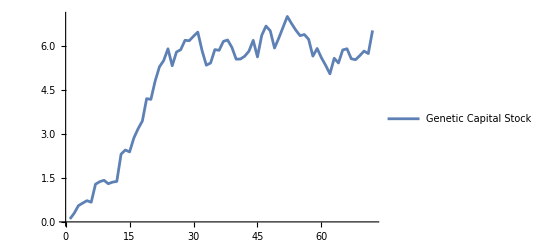

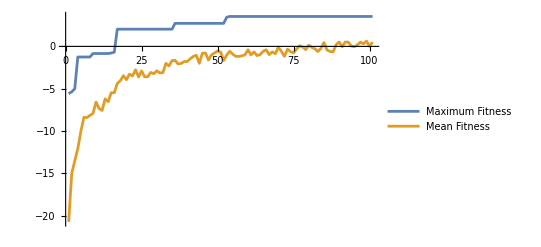

```mathematica
{KList,YList,CList,IList}=answers[fittestanswer,T];
KList;(*Capital stock at last generation*)
ListPlot[{Legended[KList,"Genetic Capital Stock"]},Joined->True,PlotRange->All](*Evolution of capital stock*)
ListPlot[{Legended[fitnessMemoryMax,"Maximum Fitness"],Legended[fitnessMemoryMean,"Mean Fitness"]},Joined->True,PlotRange->All](*Evolution of the fitness function*)
```

### Part C. Plot the evolution of the capital stock from the shooting - model and the capital stock from the genetic algorithm over time on the same graph . Also include a line to indicate the capital stock in the steady state . On another graph plot the evolution of both the savings rate from the shooting - model and the savings rate from the genetic algorithm . What do you notice?

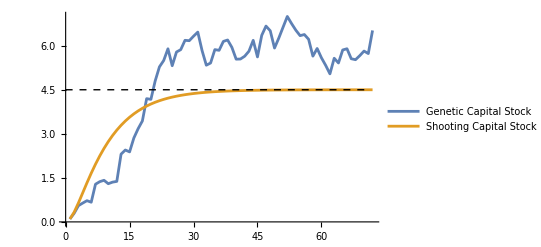

```mathematica
ListPlot[{Legended[KList,"Genetic Capital Stock"],Legended[Prepend[answerkvector,K0],"Shooting Capital Stock"]},Joined->True,Epilog->{Dashed,Black,Line[{{0,A  (α/(1/β-1+δ))^(1/(1-α))},{71,A  (α/(1/β-1+δ))^(1/(1-α))}}]}]
(*Evolution of capital stock from shooting algorithm and genetic algorithm*)
```

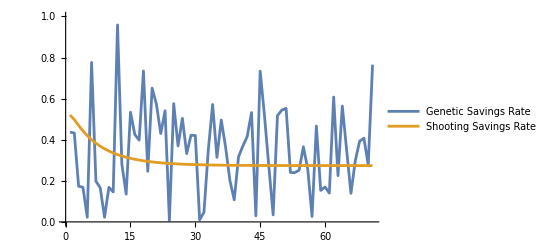

```mathematica
(*Calculations to get savings rate for the shooting algorithm using our answerkvector*)
yList=(A^(1-α)*Prepend[answerkvector,K0]^α);
IList={};
For[t=1,t<72,t++,
AppendTo[IList,Prepend[answerkvector,K0][[t+1]]-(1-δ)* Prepend[answerkvector,K0][[t]]];];
yList1=Drop[yList,{71}];
SList=IList/yList1;
ListPlot[{Legended[fittestanswer,"Genetic Savings Rate"],Legended[SList,"Shooting Savings Rate"]},Joined->True,PlotRange->{0,1}](*Evolution of savings rate from shooting model and genetic algorithm*)
```

Capital Stock Evolution : The capital stock from the shooting model (the smooth orange curve) converges steadily toward the steady state . The capital stock from the genetic algorithm (the blue curve) fluctuates more significantly and does not converge as smoothly . These fluctuations likely arise from the stochastic nature of the genetic algorithm, which introduces randomness via crossover and mutation . 
Savings Rate Evolution : The savings rate from the shooting model (orange curve) declines smoothly over time, reflecting optimal behavior determined analytically . The savings rate from the genetic algorithm (blue curve) shows much greater volatility and does not follow the smooth path of the shooting model . This again highlights the trade - off in genetic algorithms between optimization and exploration, with the randomness causing deviations from the theoretical path . Insights : The shooting model provides a smooth and predictable trajectory for both capital stock and savings rate, which aligns with theoretical expectations . The genetic algorithm introduces variability due to its probabilistic operations . While it eventually converges toward reasonable values, the fluctuations in both capital stock and savings rate highlight the less precise nature of this method . Including the steady - state line provides a clear visual reference for assessing the convergence of both approaches . The genetic algorithm, while approximating the steady state, does so with some degree of variability, unlike the shooting model, which reaches the steady state more precisely . 
Suggestions for Improvement : To reduce the fluctuations in the genetic algorithm' s results, consider : Increasing the population size . Running the algorithm for more generations . Adjusting the mutation rate (e . g ., lowering it slightly) .